```mathematica
match1={{Xari,Elien,Louise,Kaat},
{Louise,Fiebe,Xari,Leonie},
{Leonie,Dieuw,Caroline,Fiebe},
{Caroline,Dieuw,Leonie,Elien},
{Kaat,Louise,Elien,Xari}
}
```

{{Xari,Elien,Louise,Kaat},{Louise,Fiebe,Xari,Leonie},{Leonie,Dieuw,Caroline,Fiebe},{Caroline,Dieuw,Leonie,Elien},{Kaat,Louise,Elien,Xari}}

```mathematica
match2={{Leonie,Dieuw,Lena,Caroline},
{Xari,Kaat,Elien,Sofia},
{Louise,Dieuw, Leonie, Fiebe},
{Lena, Xari, Caroline, Sofia},
{Louise, Kaat, Elien, Fiebe}
}
```

{{Leonie,Dieuw,Lena,Caroline},{Xari,Kaat,Elien,Sofia},{Louise,Dieuw,Leonie,Fiebe},{Lena,Xari,Caroline,Sofia},{Louise,Kaat,Elien,Fiebe}}

```mathematica
match3={{Lena,Kaat,Xari,Sofia},
{Leonie,Fiebe,Caroline,Dieuw},
{Lena,Kaat,Leonie,Dieuw},
{Caroline,Fiebe,Xari,Sofia},
{Lena,Xari,Louise,Dieuw,Caroline}
}
```

{{Lena,Kaat,Xari,Sofia},{Leonie,Fiebe,Caroline,Dieuw},{Lena,Kaat,Leonie,Dieuw},{Caroline,Fiebe,Xari,Sofia},{Lena,Xari,Louise,Dieuw,Caroline}}

```mathematica
match4={{Lena,Elien, Dieuw, Sofia},
{Caroline,Kaat,Louise,Xari},
{Sappho,Louise,Kaat,Lena},
{Sofia,Elien,Caroline,Xari},
{Sappho,Dieuw,Lena, Xari, Kaat, Elien}
}
```

{{Lena,Elien,Dieuw,Sofia},{Caroline,Kaat,Louise,Xari},{Sappho,Louise,Kaat,Lena},{Sofia,Elien,Caroline,Xari},{Sappho,Dieuw,Lena,Xari,Kaat,Elien}}

```mathematica
match5={{Leonie,Caroline,Sappho,Elien},
{Lena,Sappho,Kaat,Dieuw},
{Lena,Dieuw,Leonie,Fiebe},
{Caroline,Elien,Kaat,Fiebe},
{Caroline,Fiebe,Dieuw,Lena},
{Lena,Leonie,Elien,Kaat}
}
```

{{Leonie,Caroline,Sappho,Elien},{Lena,Sappho,Kaat,Dieuw},{Lena,Dieuw,Leonie,Fiebe},{Caroline,Elien,Kaat,Fiebe},{Caroline,Fiebe,Dieuw,Lena},{Lena,Leonie,Elien,Kaat}}

```mathematica
MatchToCouple[match_]:=Flatten[Table[
Map[Sort,Subsets[m,{2}]]
,{m,match}
],1]
```

```mathematica
UndirectedEdge
```

UndirectedEdge

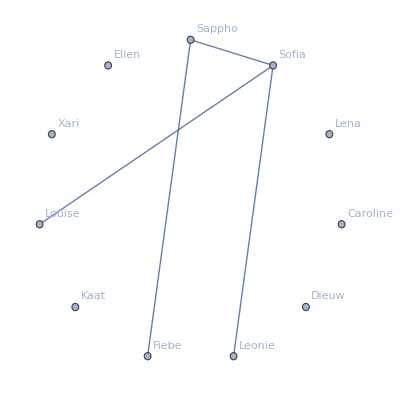

```mathematica
GraphComplement[Graph[Map[#[[1]]<->#[[2]]&,MatchToCouple[
Join[match1,match2,match3,match4,match5]]],VertexLabels->"Name",GraphLayout->"CircularEmbedding"],VertexLabels->"Name"]
```

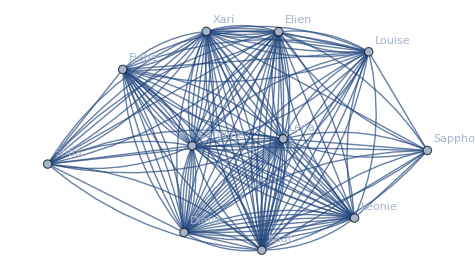

```mathematica
all=Graph[Map[#[[1]]<->#[[2]]&,MatchToCouple[
Join[match1,match2,match3,match4,match5]]],VertexLabels->"Name"]
```

```mathematica
GraphComplement[all, VertexLabels->"Name"]
```

-Graphics-

```mathematica
With   [{countperEdge=Tally[Map[#[[1]]<->#[[2]]&,MatchToCouple[
Join[match1,match2,match3,match4]]]]},
Map[#[[1]]->Thickness[1/(10*(#[[2]]))]&,countperEdge]]
```

{Elien<->Xari→Thickness[1/50],Louise<->Xari→Thickness[1/50],Kaat<->Xari→Thickness[1/60],Elien<->Louise→Thickness[1/30],Elien<->Kaat→Thickness[1/50],Kaat<->Louise→Thickness[1/50],Fiebe<->Louise→Thickness[1/30],Leonie<->Louise→Thickness[1/20],Fiebe<->Xari→Thickness[1/20],Fiebe<->Leonie→Thickness[1/40],Leonie<->Xari→Thickness[1/10],Dieuw<->Leonie→Thickness[1/60],Caroline<->Leonie→Thickness[1/40],Caroline<->Dieuw→Thickness[1/50],Dieuw<->Fiebe→Thickness[1/30],Caroline<->Fiebe→Thickness[1/30],Caroline<->Elien→Thickness[1/20],Dieuw<->Elien→Thickness[1/30],Elien<->Leonie→Thickness[1/10],Lena<->Leonie→Thickness[1/20],Dieuw<->Lena→Thickness[1/50],Caroline<->Lena→Thickness[1/30],Sofia<->Xari→Thickness[1/50],Kaat<->Sofia→Thickness[1/20],Elien<->Sofia→Thickness[1/30],Dieuw<->Louise→Thickness[1/20],Lena<->Xari→Thickness[1/40],Lena<->Sofia→Thickness[1/30],Caroline<->Xari→Thickness[1/50],Caroline<->Sofia→Thickness[1/30],Fiebe<->Kaat→Thickness[1/10],Elien<->Fiebe→Thickness[1/10],Kaat<->Lena→Thickness[1/40],Kaat<->Leonie→Thickness[1/10],Dieuw<->Kaat→Thickness[1/20],Fiebe<->Sofia→Thickness[1/10],Lena<->Louise→Thickness[1/20],Dieuw<->Xari→Thickness[1/20],Caroline<->Louise→Thickness[1/20],Elien<->Lena→Thickness[1/20],Dieuw<->Sofia→Thickness[1/10],Caroline<->Kaat→Thickness[1/10],Louise<->Sappho→Thickness[1/10],Kaat<->Sappho→Thickness[1/20],Lena<->Sappho→Thickness[1/20],Dieuw<->Sappho→Thickness[1/10],Sappho<->Xari→Thickness[1/10],Elien<->Sappho→Thickness[1/10]}

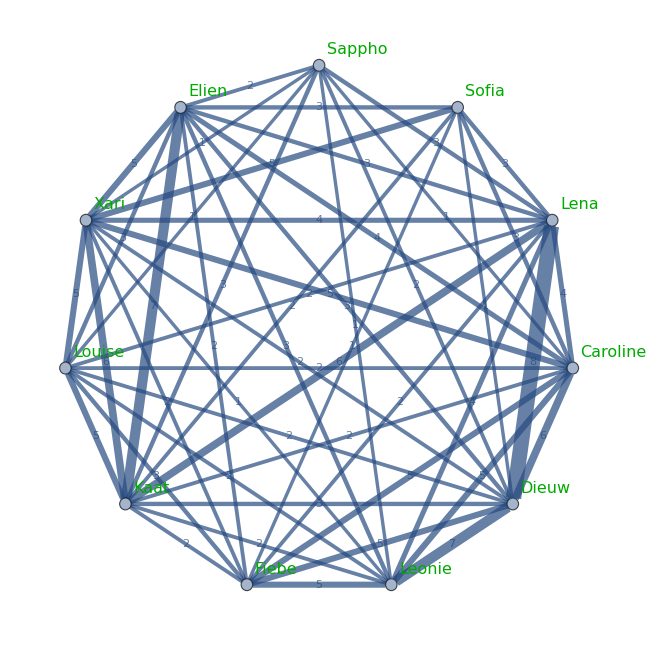

```mathematica
With   [{countperEdge=Tally[Map[#[[1]]<->#[[2]]&,MatchToCouple[
Join[match1,match2,match3,match4,match5]]]]},
Graph[Map[Labeled[#[[1]],Framed[Style[#[[2]],16,Red,Bold],Background->White]]&,countperEdge], EdgeStyle->Map[#[[1]]->Thickness[1/(30*(10-#[[2]]))]&,countperEdge],
VertexLabels->Map[#-> Framed[#,Background->White]&,DeleteDuplicates[Flatten[Join[match1,match2,match3,match4,match5]]]],
VertexLabelStyle->Directive[Darker[Green],Italic,16],GraphLayout->"CircularEmbedding"]]
```

```mathematica
Adj[g_]:=MatrixForm[AdjacencyMatrix[g],TableHeadings->{VertexList[g],Map[Rotate[#,Pi/2]&, VertexList[g]]}]
```

```mathematica
Adj[all]
```

( | Elien | Xari | Louise | Kaat | Fiebe | Leonie | Dieuw | Caroline | Lena | Sofia | Sappho
Elien | 0 | 5 | 3 | 7 | 2 | 3 | 3 | 4 | 3 | 3 | 2
Xari | 5 | 0 | 5 | 6 | 2 | 1 | 2 | 5 | 4 | 5 | 1
Louise | 3 | 5 | 0 | 5 | 3 | 2 | 2 | 2 | 2 | 0 | 1
Kaat | 7 | 6 | 5 | 0 | 2 | 2 | 3 | 2 | 6 | 2 | 3
Fiebe | 2 | 2 | 3 | 2 | 0 | 5 | 5 | 5 | 2 | 1 | 0
Leonie | 3 | 1 | 2 | 2 | 5 | 0 | 7 | 5 | 4 | 0 | 1
Dieuw | 3 | 2 | 2 | 3 | 5 | 7 | 0 | 6 | 8 | 1 | 2
Caroline | 4 | 5 | 2 | 2 | 5 | 5 | 6 | 0 | 4 | 3 | 1
Lena | 3 | 4 | 2 | 6 | 2 | 4 | 8 | 4 | 0 | 3 | 3
Sofia | 3 | 5 | 0 | 2 | 1 | 0 | 1 | 3 | 3 | 0 | 0
Sappho | 2 | 1 | 1 | 3 | 0 | 1 | 2 | 1 | 3 | 0 | 0)

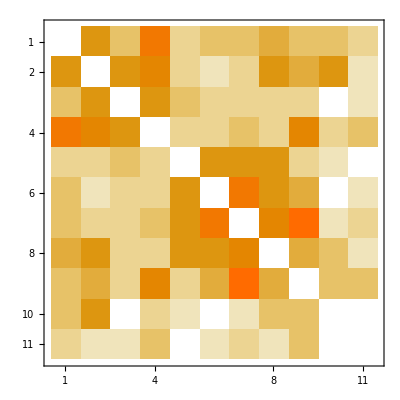

```mathematica
MatrixPlot[AdjacencyMatrix[all]]
```

```mathematica
Adj[all]
```

( | Elien | Xari | Louise | Kaat | Fiebe | Leonie | Dieuw | Caroline | Lena | Sofia | Sappho
Elien | 0 | 5 | 3 | 7 | 2 | 3 | 3 | 4 | 3 | 3 | 2
Xari | 5 | 0 | 5 | 6 | 2 | 1 | 2 | 5 | 4 | 5 | 1
Louise | 3 | 5 | 0 | 5 | 3 | 2 | 2 | 2 | 2 | 0 | 1
Kaat | 7 | 6 | 5 | 0 | 2 | 2 | 3 | 2 | 6 | 2 | 3
Fiebe | 2 | 2 | 3 | 2 | 0 | 5 | 5 | 5 | 2 | 1 | 0
Leonie | 3 | 1 | 2 | 2 | 5 | 0 | 7 | 5 | 4 | 0 | 1
Dieuw | 3 | 2 | 2 | 3 | 5 | 7 | 0 | 6 | 8 | 1 | 2
Caroline | 4 | 5 | 2 | 2 | 5 | 5 | 6 | 0 | 4 | 3 | 1
Lena | 3 | 4 | 2 | 6 | 2 | 4 | 8 | 4 | 0 | 3 | 3
Sofia | 3 | 5 | 0 | 2 | 1 | 0 | 1 | 3 | 3 | 0 | 0
Sappho | 2 | 1 | 1 | 3 | 0 | 1 | 2 | 1 | 3 | 0 | 0)